# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.995,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.995,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_]:=Module[{iansatz,nansatz,simpncirc,uapprox,uvc,uec,fdist},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];

iansatz=Reverse[ansatz]/.(-θvars);
nansatz=noisyAnsatz[iansatz,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
uapprox=CalcCircuitMatrix[simpncirc];
(* fidelity distance *)
uvc=Flatten@ConjugateTranspose@unitary;
Print[Length@uapprox,Length@uvc];
uec=#.uvc&/@uapprox;
fdist=Total[Chop[#*Conjugate[#]]&/@uec]/Length@uec;
Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[iansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist];
{time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}
]
```

## Compilation : QFT3

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

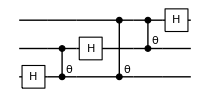

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→3,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.995,EFSingle→{1,0},RabiFreq→10,FidTwo→0.995,EFTwo→{1,0},TwoGateFreq→10}

```mathematica
qft3e05=Table[
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,4];
Print["trial ",i,varMeanInitStates[conf]];
CompileCirc[conf,unitary,qubitsnum]
,{i,10}];
```

trial 1<|1→{0.499845,0.21725},2→{0,0},3→{0.63785,0.117328},4→{0.499845,0.21725}|>

Compilation with automatically generated ansatz

$Aborted

```mathematica
DumpSave["qft3e05",qft3e05];
```

## Compilation : QFT4

```mathematica
qubitsnum=4;
Options[ToyDevice]={
qubitsNum->qubitsnum,
T1->10^5,
T2->40,
StdPassiveNoise->True,
FidSingle->0.995,
EFSingle->{1,0},
RabiFreq->10,
FidTwo->0.995,
EFTwo->{1,0},
TwoGateFreq->10
};
```

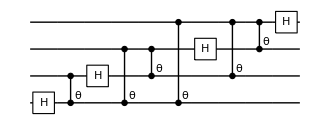

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→4,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.995,EFSingle→{1,0},RabiFreq→10,FidTwo→0.995,EFTwo→{1,0},TwoGateFreq→10}

```mathematica
(*Test for the variety of the initial states:Here's around 7*)
Table[
conf=DefaultConfig[dev,unitary,7];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
Print[i,":",a];
{ToString[i]<>ToString[Reverse@Sort[Length/@a]]}
,{i,20}]//TableForm
```

1:{{0.0260508},{0.0115487},{0.0541593},{0.00511849},{0.0116821},{0.0538941,0.0538941}}

2:{{0.0487064},{0.00276653},{0.0538941},{0.0282187},{0.0260459},{0.0541593},{0.000106183}}

3:{{0,0},{0.0487064},{0.00491381},{0.0667396},{0.0541593},{0.0199868}}

4:{{0.00276653,0.00276653},{0.0181157},{0.00511849},{0.000018584,0},{0.0541593}}

5:{{0,0},{0.000106183},{0.029027},{0.012773},{0.00511849},{0.00276653}}

6:{{0.0482106,0.0482106},{0.0541593},{0.00511849},{0.0117018},{0.00583682},{0.0028228}}

7:{{0.0487064},{0.00276653,0.00276653},{0},{0.0482106},{0.000106183},{0.0115487}}

8:{{0,0.000018584,0},{0.000106183},{0.0378143},{0.0175597},{0.0028228}}

9:{{0.0028228},{0.0199868},{0.0404509},{0.00511849},{0},{0.0181157},{0.0260459}}

10:{{0.0667396},{0.0541593},{0.00276653,0.0028228,0.00276653},{0.0378143},{0.00583682}}

11:{{0.0169425},{0.0404509},{0.0378143},{0.00984488},{0,0,0}}

12:{{0.0378143},{0},{0.00511849},{0.0260459},{0.0487064,0.0487064},{0.0541593}}

13:{{0.000106183,0.000018584},{0,0},{0.0181157},{0.0378143},{0.0667396}}

14:{{0.0105271},{0},{0.00276653,0.0028228,0.0028228},{0.0260476},{0.0117018}}

15:{{0.0667396},{0.00514392,0.00511849},{0.00276653},{0.0541593},{0.0404509},{0.0487064}}

16:{{0.0254886},{0.00276653,0.00276653,0.00276653},{0.0538941},{0.00491381},{0}}

17:{{0,0},{0.0278236},{0.00276653,0.0028228},{0.00984488},{0.0487064}}

18:{{0.00583682},{0,0,0,0},{0.0538941},{0.00925872}}

19:{{0.00491381},{0.0260459},{0.000018584,0.000106183,0},{0.0169425},{0.0404509}}

20:{{0.0175597},{0.0199868},{0.0116821},{0.0260476},{0.00276653},{0.0538941},{0.0482106}}

1{2, 1, 1, 1, 1, 1}
2{1, 1, 1, 1, 1, 1, 1}
3{2, 1, 1, 1, 1, 1}
4{2, 2, 1, 1, 1}
5{2, 1, 1, 1, 1, 1}
6{2, 1, 1, 1, 1, 1}
7{2, 1, 1, 1, 1, 1}
8{3, 1, 1, 1, 1}
9{1, 1, 1, 1, 1, 1, 1}
10{3, 1, 1, 1, 1}
11{3, 1, 1, 1, 1}
12{2, 1, 1, 1, 1, 1}
13{2, 2, 1, 1, 1}
14{3, 1, 1, 1, 1}
15{2, 1, 1, 1, 1, 1}
16{3, 1, 1, 1, 1}
17{2, 2, 1, 1, 1}
18{4, 1, 1, 1}
19{3, 1, 1, 1, 1}
20{1, 1, 1, 1, 1, 1, 1}

```mathematica
qft4e05=Table[
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,7];
Print["trial ",i,varMeanInitStates[conf]];
CompileCirc[conf,unitary,qubitsnum]
,{i,10}];
```

```mathematica
DumpSave["qft4e05",qft4e05];
```

## Compilation : QFT5

```mathematica
qubitsnum=5;
Options[ToyDevice]={
qubitsNum->qubitsnum,
T1->10^5,
T2->40,
StdPassiveNoise->True,
FidSingle->0.995,
EFSingle->{1,0},
RabiFreq->10,
FidTwo->0.995,
EFTwo->{1,0},
TwoGateFreq->10
};
```

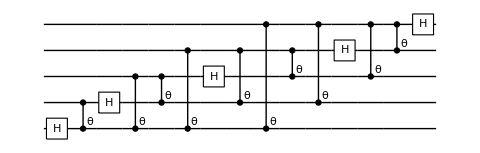

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Options@ToyDevice
```

{qubitsNum→5,T1→100000,T2→40,StdPassiveNoise→True,FidSingle→0.995,EFSingle→{1,0},RabiFreq→10,FidTwo→0.995,EFTwo→{1,0},TwoGateFreq→10}

```mathematica
(*Test for the variety of the initial states:Here's around 15*)
Table[
conf=DefaultConfig[dev,unitary,15];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
{ToString[i]<>ToString[Reverse@Sort[Length/@a]]}
,{i,20}]//TableForm
```

1{3, 2, 2, 2, 1, 1, 1, 1, 1, 1}
2{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
3{3, 3, 1, 1, 1, 1, 1, 1, 1, 1, 1}
4{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
5{3, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
6{3, 3, 2, 1, 1, 1, 1, 1, 1, 1}
7{3, 2, 2, 1, 1, 1, 1, 1, 1, 1, 1}
8{4, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
9{4, 2, 2, 1, 1, 1, 1, 1, 1, 1}
10{1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
11{2, 2, 2, 2, 1, 1, 1, 1, 1, 1, 1}
12{2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
13{4, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1}
14{2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
15{2, 2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1}
16{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
17{4, 2, 2, 1, 1, 1, 1, 1, 1, 1}
18{2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
19{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}
20{2, 2, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}

```mathematica
qft5e05=Table[
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,15];
Print["trial ",i,varMeanInitStates[conf]];
CompileCirc[conf,unitary,qubitsnum]
,{i,10}];
```

```mathematica
DumpSave["qft5e05",qft5e05];
```